```mathematica
n = 66
```

66

```mathematica
y = {28,26,33,24,34,-44,27,16,40,-2,29,22,24,21,25,30,23,29,31,19,24,20,36,32,36,28,25,21,28,29,37,25,28,26,30,32,36,26,30,22,36,23,27,27,28,27,31,27,26,33,26,32,32,24,39,28,24,25,32,25,29,27,28,29,16,23}
```

{28,26,33,24,34,-44,27,16,40,-2,29,22,24,21,25,30,23,29,31,19,24,20,36,32,36,28,25,21,28,29,37,25,28,26,30,32,36,26,30,22,36,23,27,27,28,27,31,27,26,33,26,32,32,24,39,28,24,25,32,25,29,27,28,29,16,23}

```mathematica
(*improper prior*)
```

```mathematica
pbeta[b_]:=1*Boole[-100 <= b <= 100]
```

```mathematica
psigma[s_]:=1*Boole[0 < s <= 100]
```

```mathematica
pu[b_,s_]:= pbeta[b]psigma[s]
```

```mathematica
L[b_,s_, y_]:=PDF[NormalDistribution[b, s], y]
```

```mathematica
For[i=1, i<=n,i++, 
pu[b_, s_]=pu[b, s] * L[b,s, y[[i]]];
Print[N[L[15, 10, y[[i]]]]]
]
```

0.0171369

0.0217852

0.00789502

0.0266085

0.00656158

1.10158×10^-9

0.0194186

0.0396953

0.00175283

0.00940491

0.0149727

0.0312254

0.0266085

0.0333225

0.0241971

0.0129518

0.0289692

0.0149727

0.0110921

0.036827

0.0266085

0.0352065

0.00439836

0.00940491

0.00439836

0.0171369

0.0241971

0.0333225

0.0171369

0.0149727

0.00354746

0.0241971

0.0171369

0.0217852

0.0129518

0.00940491

0.00439836

0.0217852

0.0129518

0.0312254

0.00439836

0.0289692

0.0194186

0.0194186

0.0171369

0.0194186

0.0110921

0.0194186

0.0217852

0.00789502

0.0217852

0.00940491

0.00940491

0.0266085

0.00223945

0.0171369

0.0266085

0.0241971

0.00940491

0.0241971

0.0149727

0.0194186

0.0171369

0.0149727

0.0396953

0.0289692

```mathematica
Plot3D[pu[b,s], {b, -50, 50}, {s, -10, 10}]
```

General::munfl: Exp[-1954.46] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
norm = Integrate[pu[b,s], {b, -∞, ∞},{s, 0, ∞}]
```

1/(17179869184 π^33)(-(188266767222425230164355415821394862065118851248673142024912800257533459129924873960812784279266602936960014534832846298854448203191539986758520356574461973272829547618702681075756886071269112218270229515023206975777633966155168059113476583/(3527966609377121153873899134589080386114765172792257418972167658630087457620145424114390974724192602619167313991610968987383926814114367436419137731513804602118912935973087386600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(264713/5000)))-7634092731692640510238077348842152279329001874782006995861839275393976890271206805124915184437533286263015527608189224474189614806257922270031946328299436752180676983380762583855362233529588066141968208049138098355223998797400791813/(155756197837390521822378772892973309966580767613605372790202229960859731166471800329226247143098379213033617745415632669824012984916335207950468511708602959378947887210275835031003400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(91713/5000))+(14188077998640584162122524703930527914347099897180078670593988789608888681663624100833226075393573686652373193900335233410852573880184152188192590717963871703608779650018928157869908001800409589529397220217 √(33 π) (Erf[487/(20 √33)]+Erf[833/(20 √33)]))/(186979767202026373719533987410076446173225926387005104976229917692572134917758064803538014799282809736271438939782762587867362990821902987046965391551664445024435220000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(123833/330000))+(2956451637707539869755483462728325345073019655897501790173593362072478034743457794441331074202696797775769592799311177050568567481069010348044304858091244796494853359863137144607895169043191309103248730207405100887276467267963635 Gamma[65/2,91713/5000])/(602489522757688930852620039393239636544386122249497502791945379862079750222925424384443302977903002775022458226837736548641354374447601281502871913782102713636508327122325559747468236289208927553905555824480666396970873951451415729988664226555936604213698627418591411763394105797877553376504755878946026863194294827921503221327627966761402368 √183426)+(21366187676747856550997508809214671919587644270417060127884833156717238872520539294431310984318816848198297084367522630329872592944328937479432337811324781550972943959945562698582715790489793911681251038388858306449497633475633807756720344495 Gamma[65/2,264713/5000])/(2562911286456230112763857688198586201635465894933803194831274970721530527485922397886587179428263585410036013419396197542377187447273224972153352702085733870626340351804167225795474779725351996641847391817662827813865138194834397468045332784296144178997292067557334288504603378140978935375906737320404441058098730744369301000514136996572853116462142849024 √529426))

```mathematica
p[b_,s_]:=pu[b,s]/norm
```

```mathematica
pbetamargin[b_] = Integrate[p[b,s], {s, 0, ∞}]
```

Piecewise[{{Gamma[65/2,(26426-1730 b+33 b^2)/10000]/((26426-1730 b+33 b^2)^(65/2) (-(188266767222425230164355415821394862065118851248673142024912800257533459129924873960812784279266602936960014534832846298854448203191539986758520356574461973272829547618702681075756886071269112218270229515023206975777633966155168059113476583/(3527966609377121153873899134589080386114765172792257418972167658630087457620145424114390974724192602619167313991610968987383926814114367436419137731513804602118912935973087386600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(264713/5000)))-7634092731692640510238077348842152279329001874782006995861839275393976890271206805124915184437533286263015527608189224474189614806257922270031946328299436752180676983380762583855362233529588066141968208049138098355223998797400791813/(155756197837390521822378772892973309966580767613605372790202229960859731166471800329226247143098379213033617745415632669824012984916335207950468511708602959378947887210275835031003400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(91713/5000))+(14188077998640584162122524703930527914347099897180078670593988789608888681663624100833226075393573686652373193900335233410852573880184152188192590717963871703608779650018928157869908001800409589529397220217 √(33 π) (Erf[487/(20 √33)]+Erf[833/(20 √33)]))/(186979767202026373719533987410076446173225926387005104976229917692572134917758064803538014799282809736271438939782762587867362990821902987046965391551664445024435220000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(123833/330000))+(2956451637707539869755483462728325345073019655897501790173593362072478034743457794441331074202696797775769592799311177050568567481069010348044304858091244796494853359863137144607895169043191309103248730207405100887276467267963635 Gamma[65/2,91713/5000])/(602489522757688930852620039393239636544386122249497502791945379862079750222925424384443302977903002775022458226837736548641354374447601281502871913782102713636508327122325559747468236289208927553905555824480666396970873951451415729988664226555936604213698627418591411763394105797877553376504755878946026863194294827921503221327627966761402368 √183426)+(21366187676747856550997508809214671919587644270417060127884833156717238872520539294431310984318816848198297084367522630329872592944328937479432337811324781550972943959945562698582715790489793911681251038388858306449497633475633807756720344495 Gamma[65/2,264713/5000])/(2562911286456230112763857688198586201635465894933803194831274970721530527485922397886587179428263585410036013419396197542377187447273224972153352702085733870626340351804167225795474779725351996641847391817662827813865138194834397468045332784296144178997292067557334288504603378140978935375906737320404441058098730744369301000514136996572853116462142849024 √529426))), -100≤b≤100}, {0, True}}]

```mathematica
ArgMax[pbetamargin[b],b]
```

865/33

```mathematica
MaxValue[pbetamargin[b],b]
```

(3912425457204879631503516058626198046646581314561 √(33/123833) Gamma[65/2,123833/330000])/(9348988360101318685976699370503822308661296319350255248811495884628606745887903240176900739964140486813571946989138129393368149541095149352348269577583222251221761 (-(188266767222425230164355415821394862065118851248673142024912800257533459129924873960812784279266602936960014534832846298854448203191539986758520356574461973272829547618702681075756886071269112218270229515023206975777633966155168059113476583/(3527966609377121153873899134589080386114765172792257418972167658630087457620145424114390974724192602619167313991610968987383926814114367436419137731513804602118912935973087386600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(264713/5000)))-7634092731692640510238077348842152279329001874782006995861839275393976890271206805124915184437533286263015527608189224474189614806257922270031946328299436752180676983380762583855362233529588066141968208049138098355223998797400791813/(155756197837390521822378772892973309966580767613605372790202229960859731166471800329226247143098379213033617745415632669824012984916335207950468511708602959378947887210275835031003400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(91713/5000))+(14188077998640584162122524703930527914347099897180078670593988789608888681663624100833226075393573686652373193900335233410852573880184152188192590717963871703608779650018928157869908001800409589529397220217 √(33 π) (Erf[487/(20 √33)]+Erf[833/(20 √33)]))/(186979767202026373719533987410076446173225926387005104976229917692572134917758064803538014799282809736271438939782762587867362990821902987046965391551664445024435220000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(123833/330000))+(2956451637707539869755483462728325345073019655897501790173593362072478034743457794441331074202696797775769592799311177050568567481069010348044304858091244796494853359863137144607895169043191309103248730207405100887276467267963635 Gamma[65/2,91713/5000])/(602489522757688930852620039393239636544386122249497502791945379862079750222925424384443302977903002775022458226837736548641354374447601281502871913782102713636508327122325559747468236289208927553905555824480666396970873951451415729988664226555936604213698627418591411763394105797877553376504755878946026863194294827921503221327627966761402368 √183426)+(21366187676747856550997508809214671919587644270417060127884833156717238872520539294431310984318816848198297084367522630329872592944328937479432337811324781550972943959945562698582715790489793911681251038388858306449497633475633807756720344495 Gamma[65/2,264713/5000])/(2562911286456230112763857688198586201635465894933803194831274970721530527485922397886587179428263585410036013419396197542377187447273224972153352702085733870626340351804167225795474779725351996641847391817662827813865138194834397468045332784296144178997292067557334288504603378140978935375906737320404441058098730744369301000514136996572853116462142849024 √529426)))

```mathematica
N[4071163182969588238049610823403807778981979318488453376621095702132404192842075240202041741203883575/(17087896287367280659160173649356416916821636178853222159576332862577757806245124400183696695492608 √123833)]
```

0.677036

```mathematica
N[%318]
```

0.634378

```mathematica
Integrate[pbetamargin[b], {b, -100, 100}]
```

1

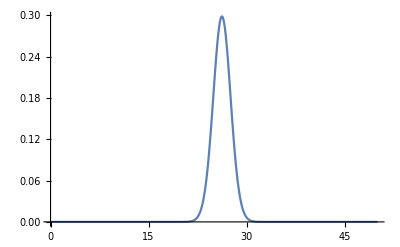

```mathematica
Plot[pbetamargin[b], {b, 0, 50}, PlotRange->All]
```

```mathematica
expbeta = Integrate[pbetamargin[b] * b, {b, -100, 100}]
```

(-(86360248146347330957967578999889840136688988205357263254609621633285264168786745653330358191900405017929479013812194876376196355223750855773259149637621377310417259175789745560078814119720518975264732927513687569719980444362188571501051174057/(61739415664099620192793234855308906757008390523864504832012934026026530508352544922001842057673370545835427994853191957279218719247001430137334910301491580537080976379529029265500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(264713/5000)))-500264410069252578890601280814277403152998986491396670561971110046605796192288403165451274249587296377211911741483970127176651428211344004059842073133212393695349175642038268803960981158343634507522954528534364731227734400257431836001/(389390494593476304555946932232433274916451919034013431975505574902149327916179500823065617857745948032584044363539081674560032462290838019876171279271507398447369718025689587577508500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(91713/5000))+(2454537493764821060047196773779981329182048282212153610012760060602337741927806969444148111043088247790860562544757995380077495281271858328557318194207749804724318879453274571311494084311470858988585719097541 √π (Erf[487/(20 √33)]+Erf[833/(20 √33)]))/(37395953440405274743906797482015289234645185277401020995245983538514426983551612960707602959856561947254287787956552517573472598164380597409393078310332889004887044000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 √33 ⅇ^(123833/330000))+(38747434342682151323310502958484870052850939429565743149235569300393680039133896017678791056580079489544490662025766935897132879931865737744431504975824273478477315966569557303519819408641419934301747967866427199177882262983300579 Gamma[65/2,91713/5000])/(301244761378844465426310019696619818272193061124748751395972689931039875111462712192221651488951501387511229113418868274320677187223800640751435956891051356818254163561162779873734118144604463776952777912240333198485436975725707864994332113277968302106849313709295705881697052898938776688252377939473013431597147413960751610663813983380701184 √183426)+(1960185854283458657822574482421133916259139182687504531429434314604893715941343895264545570157785505469475622938348376579196017806280711146663189541356118323617125407637925115483961067187749117773864504451803845928390950664098023342812303100021 Gamma[65/2,264713/5000])/(8970189502596805394673501908695051705724130632268311181909462397525356846200728392603055127998922548935126046967886691398320156065456287402536734457300068547192191231314585290284161729038731988246465871361819897348527983681920391138158664745036504626490522236450670009766111823493426273815673580621415543703345557605292553501799479488004985907617499971584 √529426))/(-(188266767222425230164355415821394862065118851248673142024912800257533459129924873960812784279266602936960014534832846298854448203191539986758520356574461973272829547618702681075756886071269112218270229515023206975777633966155168059113476583/(3527966609377121153873899134589080386114765172792257418972167658630087457620145424114390974724192602619167313991610968987383926814114367436419137731513804602118912935973087386600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(264713/5000)))-7634092731692640510238077348842152279329001874782006995861839275393976890271206805124915184437533286263015527608189224474189614806257922270031946328299436752180676983380762583855362233529588066141968208049138098355223998797400791813/(155756197837390521822378772892973309966580767613605372790202229960859731166471800329226247143098379213033617745415632669824012984916335207950468511708602959378947887210275835031003400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(91713/5000))+(14188077998640584162122524703930527914347099897180078670593988789608888681663624100833226075393573686652373193900335233410852573880184152188192590717963871703608779650018928157869908001800409589529397220217 √(33 π) (Erf[487/(20 √33)]+Erf[833/(20 √33)]))/(186979767202026373719533987410076446173225926387005104976229917692572134917758064803538014799282809736271438939782762587867362990821902987046965391551664445024435220000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 ⅇ^(123833/330000))+(2956451637707539869755483462728325345073019655897501790173593362072478034743457794441331074202696797775769592799311177050568567481069010348044304858091244796494853359863137144607895169043191309103248730207405100887276467267963635 Gamma[65/2,91713/5000])/(602489522757688930852620039393239636544386122249497502791945379862079750222925424384443302977903002775022458226837736548641354374447601281502871913782102713636508327122325559747468236289208927553905555824480666396970873951451415729988664226555936604213698627418591411763394105797877553376504755878946026863194294827921503221327627966761402368 √183426)+(21366187676747856550997508809214671919587644270417060127884833156717238872520539294431310984318816848198297084367522630329872592944328937479432337811324781550972943959945562698582715790489793911681251038388858306449497633475633807756720344495 Gamma[65/2,264713/5000])/(2562911286456230112763857688198586201635465894933803194831274970721530527485922397886587179428263585410036013419396197542377187447273224972153352702085733870626340351804167225795474779725351996641847391817662827813865138194834397468045332784296144178997292067557334288504603378140978935375906737320404441058098730744369301000514136996572853116462142849024 √529426))

```mathematica
N[%]
```

26.2121

```mathematica
CurrentValue[Cells[],InitializationCell]=True;
```